# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["/Users/pcs/Desktop/Entropy/schmidt modes/QMB.wl"];
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
cp=ResourceFunction["CombinePlots"];
```

```mathematica
Clear[Isingnoisy];
Isingnoisy[h_,g_,J_,L_] := Module[{NNIndices,A,B,ϵ=RandomVariate[NormalDistribution[0,1],L]},
NNIndices=Normal[SparseArray[Thread[{#,#+1}->3],{L}]&/@Range[L-1]];
A=-Normal[Total[{h*Pauli[#]+g*Pauli[3#]&/@IdentityMatrix[L],J*(Pauli/@NNIndices)},2]];
B=0.001*ϵ. (Pauli/@DiagonalMatrix[ConstantArray[1,L]]);
A+B];
```

# T1

```mathematica
L=10;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
g=0.5;
h=1.;
H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
```

```mathematica
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
La=L/2;
Lb=L-La;
eveneigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,uno},DistributedContexts->Full];
oddeigenvecdiag=ParallelTable[sdiag[L,La,Lb,i],{i,dos},DistributedContexts->Full];
```

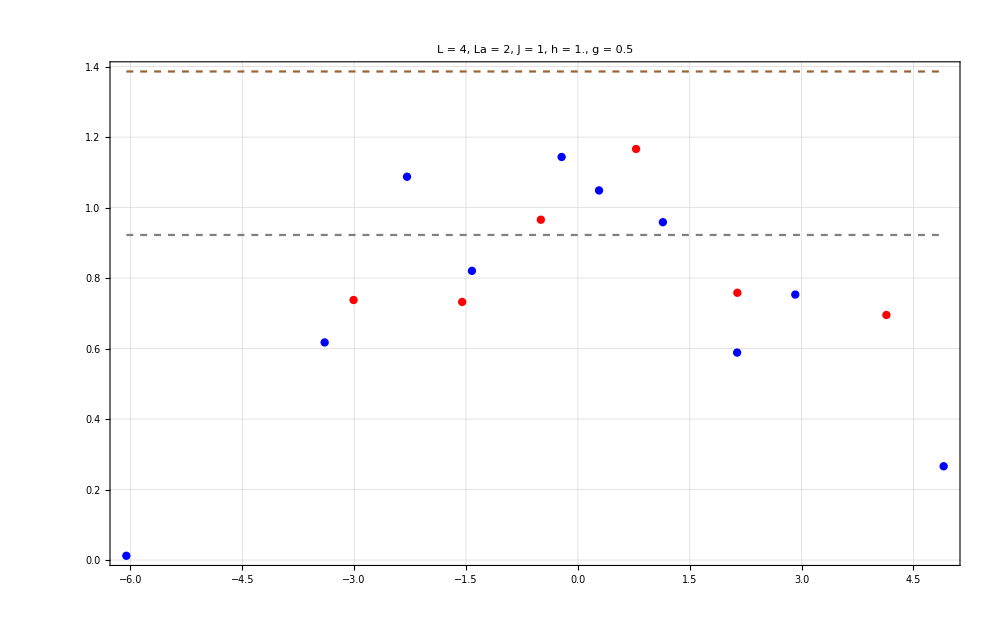

```mathematica
Show[{ListPlot[{Transpose[{eveneigenval,eveneigenvecdiag}],Transpose[{oddeigenval,oddeigenvecdiag}]},PlotStyle->{Directive[Blue,PointSize[0.006]],Directive[Red,PointSize[0.006]]},PlotRange->All,ImageSize->1000,ImageSize->800,PlotTheme->"Detailed",FrameStyle->Directive[Black,22],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black]],Plot[{N[pageEntropy[L/2,L/2]],Log[2^(L/2)]},{x,Min[allvals],Max[allvals]},PlotStyle->{Directive[Dashed,Gray],Directive[Dashed,Brown]},PlotRange->All]},PlotRange->All]
```

# SVD

```mathematica
Clear[arrayt];
arrayt[t_,val_,vec_]:=Exp[-I*val*t]*vec;
Clear[new];
new[ini_,t_,La_,val_,vec_]:=Module[{schmidt,psit,ck=Conjugate[vec] . ini,a=2^(La),b=2^(L-La),phases=arrayt[t,val,vec]},
psit=ArrayReshape[N[Total[ phases*ck  ]],{a,b}];
schmidt=Total[Map[VNentropy,(Chop[SingularValueList[psit]])^2]]
];
```

```mathematica
allstates=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstatesfull=data[[All,2]][[-10;;-1]];
```

```mathematica
tlist=Table[10^i,{i,-1,6,0.002}];
tlist//Length
```

3501

```mathematica
productstatesfull=Table[RandomChainProductState2[L],{i,20}];
```

```mathematica
productstatesfull=Table[Flatten[KroneckerProduct[Flatten[KroneckerProduct[RandomChainProductState2[L-5],RandomQubitState[]]],RandomChainProductState2[L-4]]],{i,20}];
```

```mathematica
productstatesfull=Table[RandomChainProductState[L],{i,20}];
```

```mathematica
productstatesfull=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],{i,20}];
```

```mathematica
productstatesfull=Table[Flatten[KroneckerProduct[RandomChainProductState2[L-1],RandomQubitState[]]],{i,20}];
```

```mathematica
entropy2=ParallelTable[{t,new[j,t,L,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
```

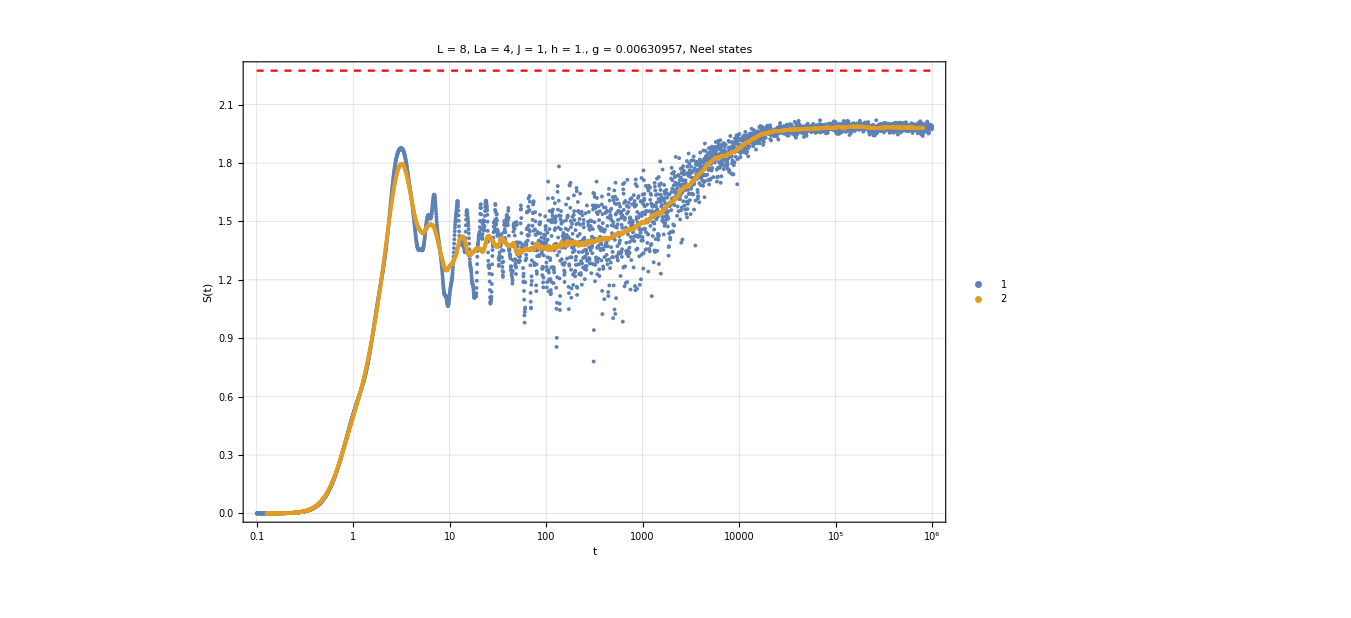

```mathematica
Show[{ListLogLinearPlot[{Mean[entropy2],MovingAverage[Mean[entropy2],100]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Neel states ",35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[pageEntropy[L/2,L/2],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All]
```

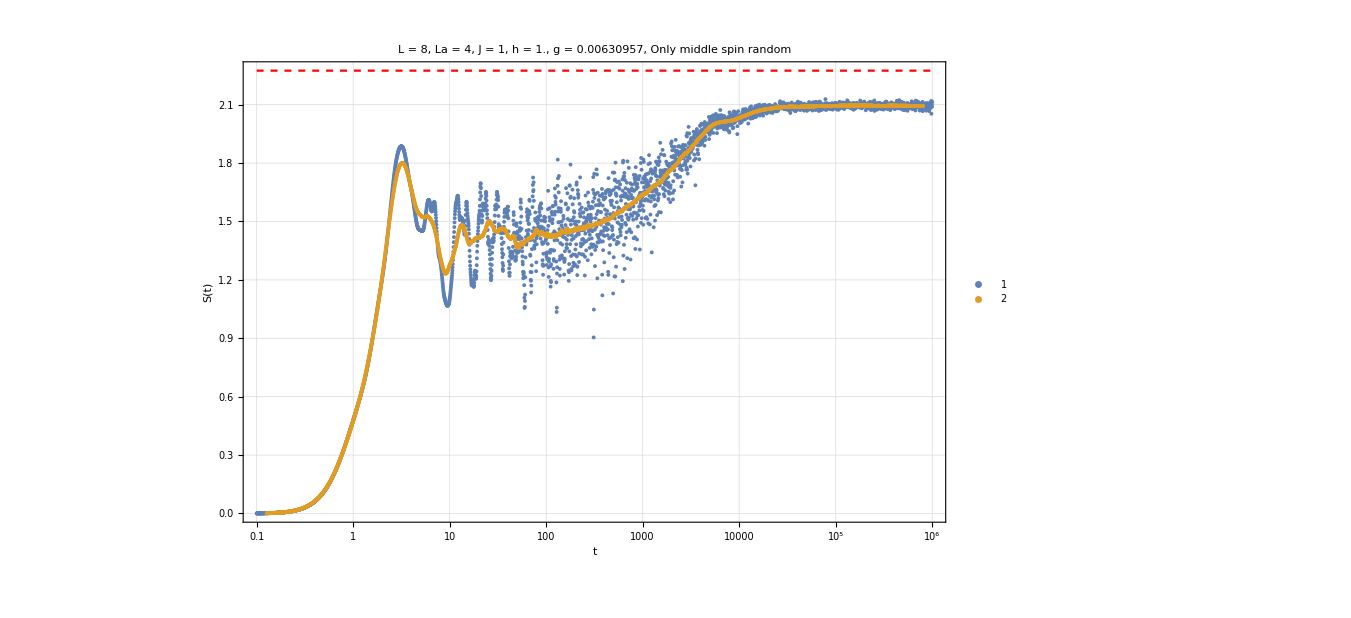

```mathematica
Show[{ListLogLinearPlot[{Mean[entropy2],MovingAverage[Mean[entropy2],100]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Only middle spin random ",35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[pageEntropy[L/2,L/2],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All]
```

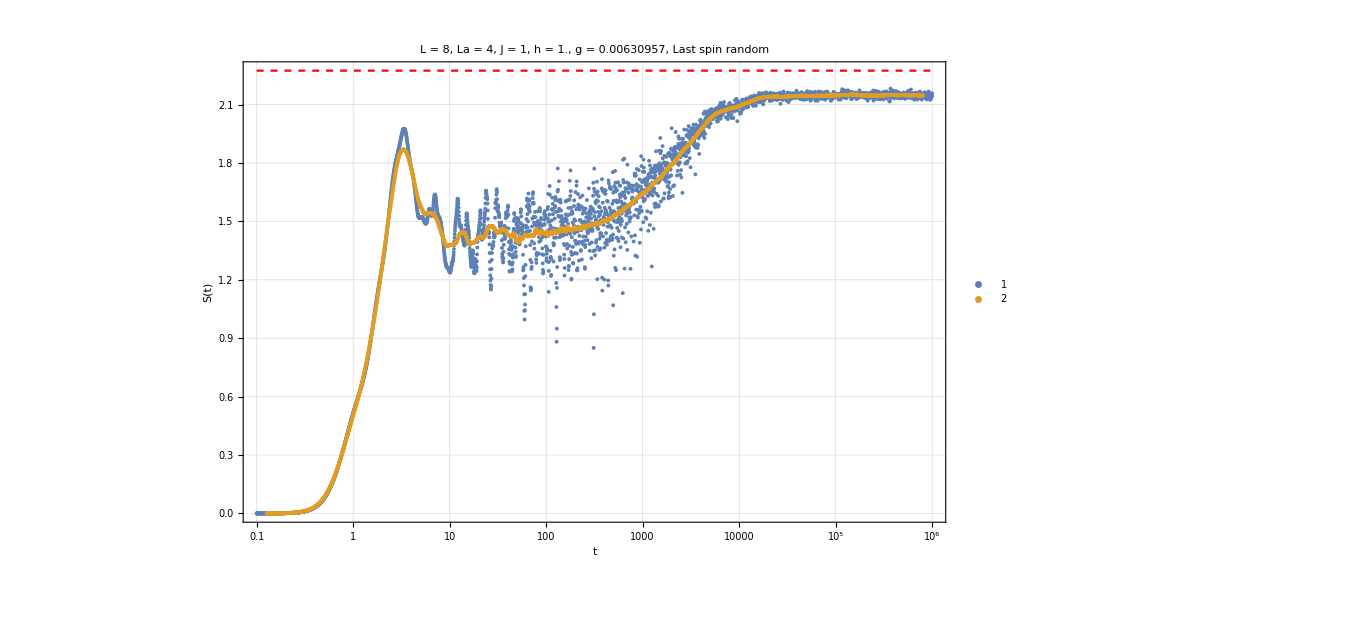

```mathematica
Show[{ListLogLinearPlot[{Mean[entropy2],MovingAverage[Mean[entropy2],100]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Last spin random ",35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[pageEntropy[L/2,L/2],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All]
```

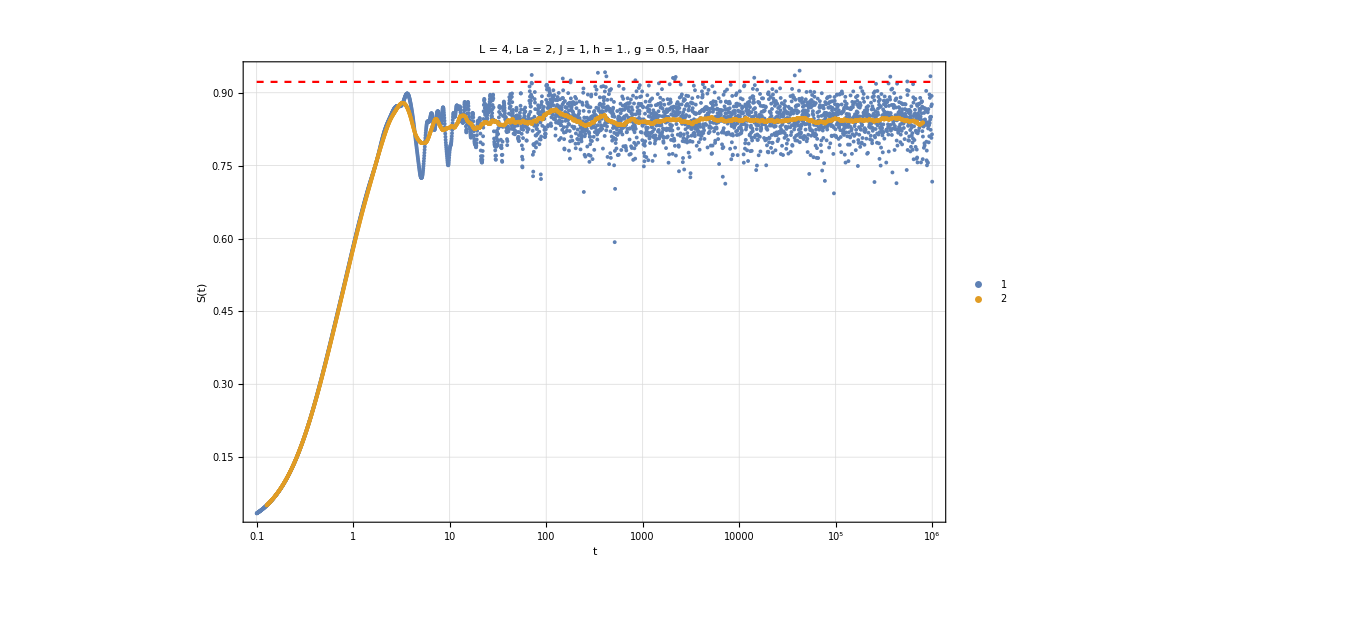

```mathematica
Show[{ListLogLinearPlot[{Mean[entropy2],MovingAverage[Mean[entropy2],100]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]]<>", Haar ",35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[pageEntropy[L/2,L/2],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->All]
```

## Cycle

```mathematica
J=1;
h=1;
```

```mathematica
glist=Table[10^i,{i,-4,0,0.05}];
glist//Length
```

81

```mathematica
tlist=Table[10^i,{i,0,7,0.001}];
tlist//Length
```

7001

```mathematica
plots={};
plots2={};
Do[

H=IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

allstates=Table[RandomChainProductState[L],1000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[allvecs].i]^4]],{i,allstates},DistributedContexts->Full];
data=SortBy[Transpose[{1/iprs,allstates}],First];
productstatesfull=data[[All,2]][[-10;;-1]];

entropy2=ParallelTable[{t,new[j,t,L,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full,Method->"CoarsestGrained"];

plot2=Show[{ListLogLinearPlot[Mean[entropy2],PlotRange->{{tlist[[1]],tlist[[-1]]},{0,pageEntropy[La,Lb]+0.1}},Joined->False,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", g = "<>ToString[N[g]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]},PlotLegends->Automatic],LogLinearPlot[pageEntropy[L/2,L/2],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]}];
Export["mean_plots_L_"<>ToString[L]<>"_h_1_g_"<>ToString[N[g]]<>"_.png",plot2];
AppendTo[plots2,plot2];

,{g,glist}];
```

```mathematica
ListAnimate[plots2,AnimationRunning->False]
```

# g -> 0

```mathematica
J=1;
h=1;
glist=Table[10^i,{i,-5,0,0.2}];
n=Length[glist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
n
```

27

```mathematica
tlist=Table[10^i,{i,-1,8,0.0025}];
tlist//Length
```

3601

```mathematica
c=N[pageEntropy[L/2,L/2]];
```

```mathematica
productstatesfull=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],50];
```

```mathematica
plots={};
alldata={};
Do[

H=IsingNNOpenHamiltonian[h,glist[[g]],J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

entropy2=ParallelTable[{t,new[j,t,L/2,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
data=MovingAverage[Mean[entropy2],100];
AppendTo[alldata,data];

,{g,Length[glist]}];
```

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of 50 Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-6,0}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[c,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of 50 Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-6,0}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[c,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

```mathematica
Export["new_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.m",alldata]
```

new_entanglemententropy_halfhaar_L_10_J_1_h_1_g.m

```mathematica
Export["new_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.png",test,ImageResolution->500]
```

new_entanglemententropy_halfhaar_L_10_J_1_h_1_g.png

## Scaling

```mathematica
alldata=Import["/Users/pcs/Desktop/Entropy/schmidt modes/new_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_1_g.m"];
```

```mathematica
newalldata=Table[Transpose[{i[[All,1]],i[[All,2]]/c}],{i,alldata}];
```

```mathematica
test=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[N[h]]<>", Average of 50 Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-6,0}},LegendLabel->Style["g = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[1,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
Export["new_entanglemententropy_normalized_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.png",test,ImageResolution->500]
```

new_entanglemententropy_normalized_halfhaar_L_10_J_1_h_1_g.png

```mathematica
(*2) Nearest sample but only if within tolerance tol;otherwise Missing["NotReached",minDistance]*)
Clear[cross];
cross[data_,v_]:=Module[{vals,m,idx,tol=0.06},vals=Abs[data[[All,2]]-v];
m=Min[vals];
If[m>tol,Missing["NotReached",m],
idx=First@FirstPosition[vals,m];
data[[idx,1]]]
]
```

```mathematica
list=Table[{glist[[i]],cross[newalldata[[i]],0.9]},{i,Length[glist]}]
```

{{0.00001,462093.},{0.0000158489,293244.},{0.0000251189,185025.},{0.0000398107,116743.},{0.0000630957,71569.7},{0.0001,46744.4},{0.000158489,31062.},{0.000251189,19598.8},{0.000398107,12295.},{0.000630957,7365.96},{0.001,4387.62},{0.00158489,2849.24},{0.00251189,1530.13},{0.00398107,965.449},{0.00630957,568.498},{0.01,316.031},{0.0158489,168.744},{0.0251189,77.1311},{0.0398107,25.3939},{0.0630957,15.3013},{0.1,9.27319},{0.158489,7.19829},{0.251189,4.54181},{0.398107,4.43843},{0.630957,4.81093},{1.,6.87431}}

```mathematica
Export["equilibration_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_"<>ToString[h]<>"_g.m",list]
```

equilibration_entanglemententropy_halfhaar_L_10_J_1_h_1_g.m

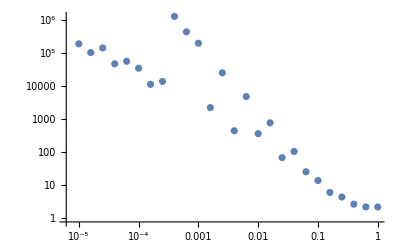

```mathematica
ListLogLogPlot[list,PlotRange->All]
```

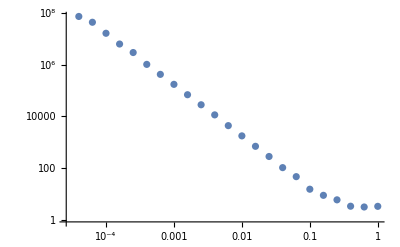

```mathematica
ListLogLogPlot[list,PlotRange->All]
```

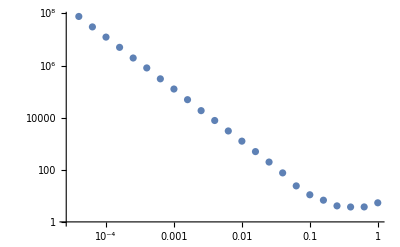

```mathematica
ListLogLogPlot[list,PlotRange->All]
```

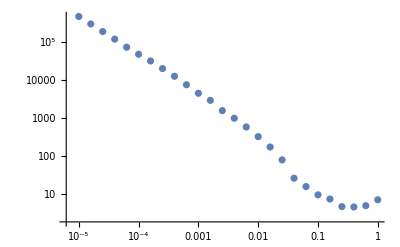

```mathematica
ListLogLogPlot[list,PlotRange->All]
```

```mathematica
info=Table[Import["/Users/pcs/Desktop/Entropy/schmidt modes/equilibration_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_h_1_g.m"],{L,{4,6,8,10}}];
```

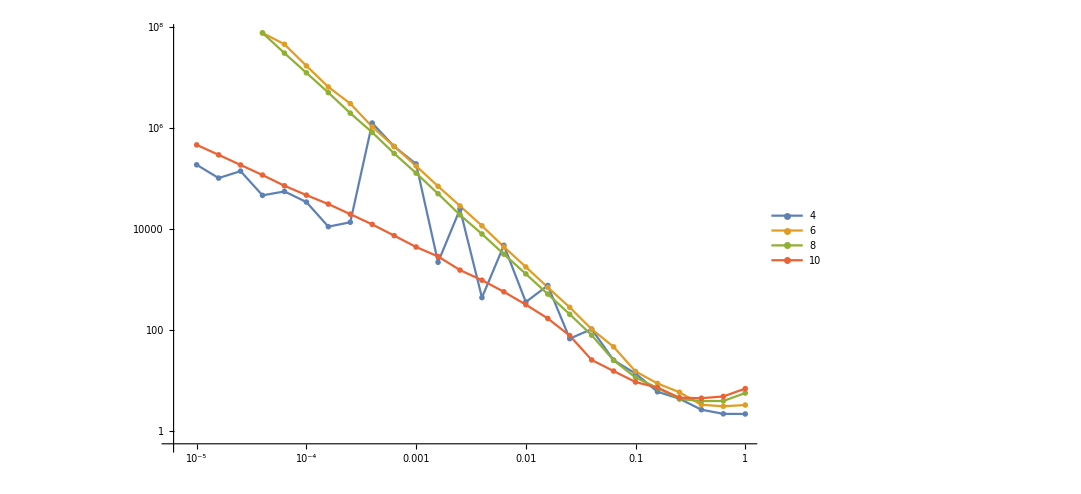

```mathematica
ListLogLogPlot[info,PlotRange->All,ImageSize->800,Joined->True,PlotMarkers->"OpenMarkers",PlotLegends->Table[L,{L,{4,6,8,10}}]]
```

# h -> 0

```mathematica
J=1;
g=1;
hlist=Table[10^i,{i,-3.5,0,0.2}];
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
n
```

19

```mathematica
tlist=Table[10^i,{i,-1,8,0.0025}];
tlist//Length
```

3601

```mathematica
c=N[pageEntropy[L/2,L/2]];
```

```mathematica
productstatesfull=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],10];
```

```mathematica
plots={};
alldata={};
Do[

H=IsingNNOpenHamiltonian[hlist[[h]],g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Heven]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[N[Hodd]]]]];
uno=ParallelTable[Beven.i,{i,eveneigenvec},DistributedContexts->Full];
dos=ParallelTable[Bodd.i,{i,oddeigenvec},DistributedContexts->Full];
allvecs=Join[uno,dos];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

entropy2=ParallelTable[{t,new[j,t,L/2,allvals,allvecs]},{j,productstatesfull},{t,tlist},DistributedContexts->Full];
data=MovingAverage[Mean[entropy2],100];
AppendTo[alldata,data];

,{h,Length[hlist]}];
```

```mathematica
test=Show[{ListLogLinearPlot[alldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[N[g]]<>", Average of 10 Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3.5,0}},LegendLabel->Style["h = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[c,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
Export["new_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_g_"<>ToString[g]<>"_h.m",alldata]
```

new_entanglemententropy_halfhaar_L_10_J_1_g_1_h.m

```mathematica
Export["new_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_g_"<>ToString[g]<>"_h.png",test,ImageResolution->500]
```

new_entanglemententropy_halfhaar_L_10_J_1_g_1_h.png

## Scaling

```mathematica
alldata=Import["/Users/pcs/Desktop/Entropy/schmidt modes/new_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_g_1_h.m"];
```

```mathematica
newalldata=Table[Transpose[{i[[All,1]],i[[All,2]]/c}],{i,alldata}];
```

```mathematica
test=Show[{ListLogLinearPlot[newalldata,PlotStyle->reds,Joined->True,ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", g = "<>ToString[N[g]]<>", Average of 10 Half Haar states",30,Black],PlotLegends->Placed[BarLegend[{cf,{-3.5,0}},LegendLabel->Style["h = 10^x", 20, Black],LabelStyle->{Black,FontSize->18}],Right]],LogLinearPlot[1,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]]},PlotRange->{{Log[tlist[[1]]],Log[tlist[[-1]]]},All}]
```

-Graphics-

```mathematica
Export["new_entanglemententropy_normalized_halfhaar_L_"<>ToString[L]<>"_J_1_g_"<>ToString[g]<>"_h.png",test,ImageResolution->500]
```

new_entanglemententropy_normalized_halfhaar_L_10_J_1_g_1_h.png

```mathematica
(*2) Nearest sample but only if within tolerance tol;otherwise Missing["NotReached",minDistance]*)
Clear[cross];
cross[data_,v_]:=Module[{vals,m,idx,tol=0.06},vals=Abs[data[[All,2]]-v];
m=Min[vals];
If[m>tol,Missing["NotReached",m],
idx=First@FirstPosition[vals,m];
data[[idx,1]]]
]
```

```mathematica
list=Table[{glist[[i]],cross[newalldata[[i]],0.6]},{i,Length[hlist]}]
```

{{0.00001,1.56577×10^7},{0.0000158489,6.19768×10^6},{0.0000251189,2.46734×10^6},{0.0000398107,982266.},{0.0000630957,391047.},{0.0001,155679.},{0.000158489,61976.8},{0.000251189,24673.4},{0.000398107,9822.66},{0.000630957,3910.47},{0.001,1556.79},{0.00158489,619.768},{0.00251189,248.159},{0.00398107,99.9377},{0.00630957,40.7126},{0.01,17.2675},{0.0158489,7.71311},{0.0251189,3.50533}}

```mathematica
Export["equilibration_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_g_"<>ToString[g]<>"_h.m",list]
```

equilibration_entanglemententropy_halfhaar_L_10_J_1_g_1_h.m

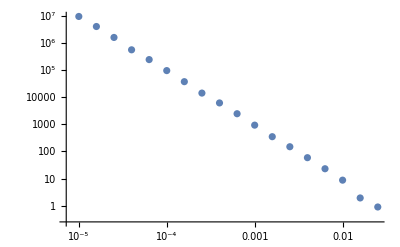

```mathematica
ListLogLogPlot[list,PlotRange->All]
```

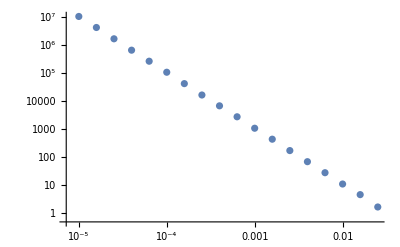

```mathematica
ListLogLogPlot[list,PlotRange->All]
```

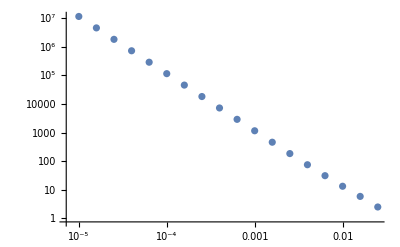

```mathematica
ListLogLogPlot[list,PlotRange->All]
```

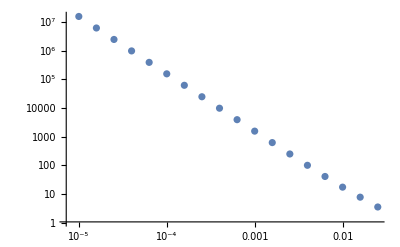

```mathematica
ListLogLogPlot[list,PlotRange->All]
```

```mathematica
info=Table[Import["/Users/pcs/Desktop/Entropy/schmidt modes/equilibration_entanglemententropy_halfhaar_L_"<>ToString[L]<>"_J_1_g_1_h.m"],{L,{4,6,8,10}}];
```

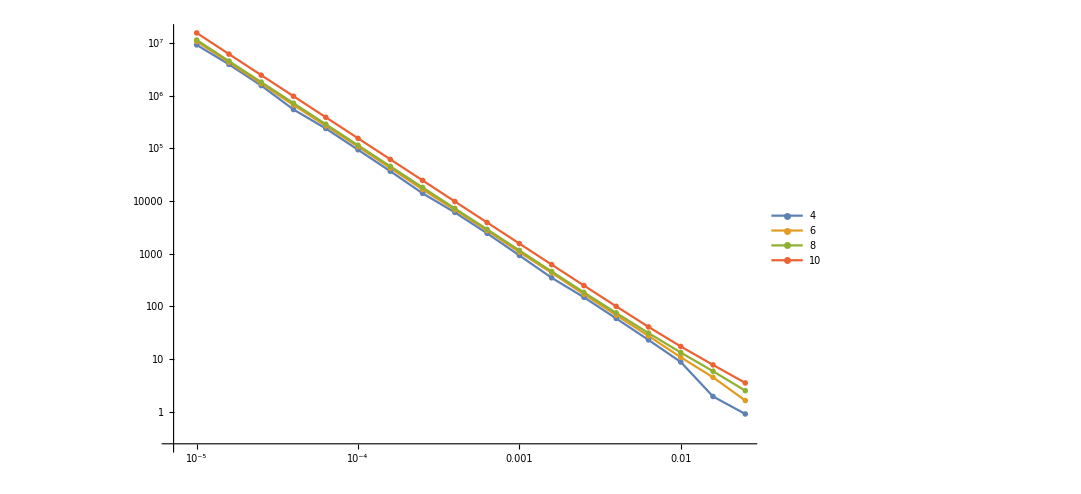

```mathematica
ListLogLogPlot[info,PlotRange->All,ImageSize->800,Joined->True,PlotMarkers->"OpenMarkers",PlotLegends->Table[L,{L,{4,6,8,10}}]]
```